# Final Review

## Master Stability Function (one-dimensional case)

Given a coupled network with linear interaction and dynamics given by f(x). We want to compute the range for the coupling strength σ such that the synchronized state is transversely stable. The equations of motion are given by:
									(ẋ)_l=f(x_l) + σ∑_m G_(l,m)x_m
Recall that the master stability function of a one-dimensional system a synchronized state z* (a fixed point) takes the form
									Γ(ξ) = f'(z*) + Re(ξ) g' (z*).
Where ξ = σ λ^(v). λ^(v) is the eigenvalue of the Laplacian matrix of the system.

						 The synchronized state is transversely stable if Γ(ξ) < 0

As an example, consider the interaction given by the following adjacency matrix

```mathematica
A = {{0, 1, 1, 1}, {1, 0, 1, 0}, {1, 1, 0, 1}, {1, 0, 1, 0}};
A // MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 0)

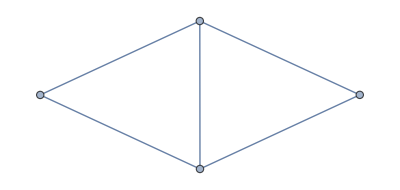

```mathematica
AdjacencyGraph[A]
```

Given the adjacency matrix, we proceed to compute the Laplacian matrix.

```mathematica
G = DiagonalMatrix[Total[A, {2}]] - A;
G // MatrixForm
```

(3 | -1 | -1 | -1
-1 | 2 | -1 | 0
-1 | -1 | 3 | -1
-1 | 0 | -1 | 2)

```mathematica
Eigenvalues[G]
```

{4,4,2,0}

Assuming a given f(x) and g(x) = x, transverse stability for the one-dimensional system reduces to 
								Γ(σ λ^(v)) = f'(x*) + σ Re( λ^(v)) g' (z*) . For v=1,2,3,4

In this example, we consider conditions for which the eigenvalue is not zero.

```mathematica
Reduce[{f'[x] + 4σ < 0, f'[x] + 2σ < 0}, σ]
```

(f'[x]≤0&&σ<-1/4 f'[x])||(f'[x]>0&&σ<-1/2 f'[x])

#### A second example

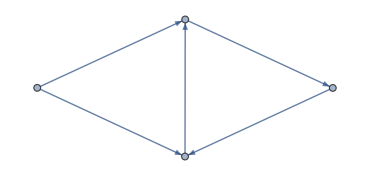

```mathematica
A = {{0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}, {1, 0, 1, 0}};
AdjacencyGraph[A]
```

```mathematica
G = DiagonalMatrix[Total[A, {2}]] - A;
G // MatrixForm
```

(1 | -1 | 0 | 0
0 | 1 | -1 | 0
-1 | 0 | 1 | 0
-1 | 0 | -1 | 2)

```mathematica
Re[Eigenvalues[G]]
```

{2,3/2,3/2,0}

The transverse-stability condition in terms of σ reads

```mathematica
Reduce[{f'[x] + 2σ <0, f'[x] + 3/2 σ <0}, σ]
```

(f'[x]≤0&&σ<-1/2 f'[x])||(f'[x]>0&&σ<-2/3 f'[x])

## Maps

```mathematica
f[x_]=Piecewise[{{x/3+3/4, 0 ≤ x ≤ 3/4}, {-4x+4, 3/4 < x ≤ 1}, {Undefined, True}}];
```

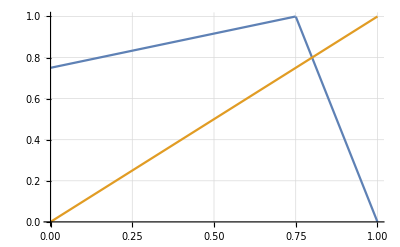

```mathematica
Plot[{f[x], x}, {x, 0, 1}, GridLines->Automatic]
```

Finding all fixed points of the map

```mathematica
Solve[f[x] == x, x]
```

{{x→4/5}}

Evaluating the intervals: Interval 1

```mathematica
f /@ {0, 3/4}
```

{3/4,1}

Interval 2

```mathematica
f /@ {3/4, 1}
```

{1,0}

#### Evaluating a second set of partitions

In this subsection, we consider the partitions I_0=[0, 3/4], I_1=[3/4, 4/5], and I_2=[4/5, 1]. We note that this set of partitions is a valid Markov partition if it maps boundaries onto boundaries:

```mathematica
boundaries = {0, 3/4, 4/5, 1};
partitions = {{0, 3/4}, {3/4, 4/5}, {4/5, 1}};
fInt = Map[f, partitions, {2}];
partitions // MatrixForm
fInt // MatrixForm
```

(0 | 3/4
3/4 | 4/5
4/5 | 1)

(3/4 | 1
1 | 4/5
4/5 | 0)

Check whether all mapped boundaries map onto boundaries

```mathematica
ArrayReduce[SubsetQ[boundaries, #] & , fInt, 2]
```

{True,True,True}

Next, we write the transition matrix

```mathematica
A = {{0, 1, 1}, {0, 0, 1}, {1, 1, 0}};
A // MatrixForm
```

(0 | 1 | 1
0 | 0 | 1
1 | 1 | 0)

```mathematica
Tr[MatrixPower[A, 2]]
```

4

```mathematica
Tr[MatrixPower[A, 3]]
```

3

```mathematica
Tr[MatrixPower[A, 4]]
```

8

```mathematica
Solve[f[f[x]] == x, x]
```

{{x→3/7},{x→4/5},{x→25/28}}

```mathematica
Tr[MatrixPower[{{0, 1}, {1,1}}, 2]]
```

3

Finally, we compute the transfer matrix of the map and compute its invariant density. To do so, we first divide each row of the adjacency matrix by its corresponding partition-slope.

```mathematica
T =Transpose[(A / {1/3, 4, 4})];
T // MatrixForm
```

(0 | 0 | 1/4
3 | 0 | 1/4
3 | 1/4 | 0)

Double check that we have an eigenvalue of 1

```mathematica
Eigenvalues[T]
```

{1,-3/4,-1/4}

Compute the size of each interval of the map

```mathematica
eigvec = {Subscript[ρ, 0],Subscript[ρ, 1], Subscript[ρ, 2]};
intSize = {3/4, 1/20, 1/5};
```

```mathematica
Solve[T . eigvec == eigvec && eigvec . intSize == 1, eigvec]
```

{{ρ_0→4/7,ρ_1→16/7,ρ_2→16/7}}

## Coupled Dynamical Systems

```mathematica
Reduce[{g[x]+2σ <0, g[x]+4σ<0},σ]
```

(g[x]≤0&&σ<-g[x]/4)||(g[x]>0&&σ<-g[x]/2)

```mathematica
g[x]
```

g[x]